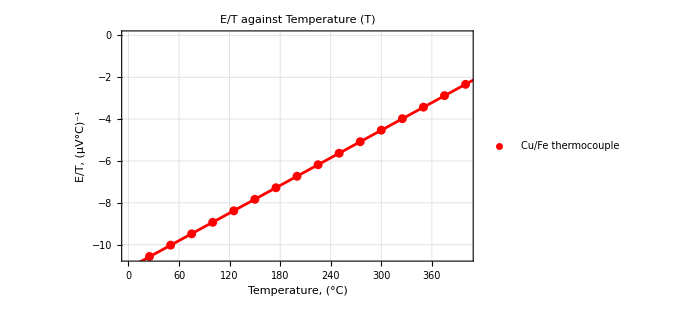
-Graphics-
Cu/Fe thermocouple: y==0.0219659 x-11.1215, Uncertainty in Slope: 0.0000104944

```mathematica
(*Define the datasets*)
t1={{25,-10.56},{50,-10.02},{75,-9.48},{100,-8.93},{125,-8.38},{150,-7.83},{175,-7.28},{200,-6.73},{225,-6.18},{250,-5.63},{275,-5.08},{300,-4.53},{325,-3.98},{350,-3.43},{375,-2.88},{400,-2.34}};

t1error={{Around[25,1],Around[-10.56,0.01]},{Around[50,1],Around[-10.02,0.01]},{Around[75,1],Around[-9.48,0.01]},{Around[100,1],Around[-8.93,0.01]},{Around[125,1],Around[-8.38,0.01]},{Around[150,1],Around[-7.83,0.01]},{Around[175,1],Around[-7.28,0.01]},{Around[200,1],Around[-6.73,0.01]},{Around[225,1],Around[-6.18,0.01]},{Around[250,1],Around[-5.63,0.01]},{Around[275,1],Around[-5.08,0.01]},{Around[300,1],Around[-4.53,0.01]},{Around[325,1],Around[-3.98,0.01]},{Around[350,1],Around[-3.43,0.01]},{Around[375,1],Around[-2.88,0.01]},{Around[400,1],Around[-2.34,0.01]}};

(*Fit linear models to the data*)
fitt1=LinearModelFit[t1,x,x];

(*Extracting uncertainties in the slope of each fit*)uncertainty1=fitt1["ParameterTableEntries"][[2,2]];

(*Extract equations as strings*)
eq1=ToString[TraditionalForm[y==fitt1["BestFit"]]];

(*Existing code for plotting*)Column[{combinedPlot=Show[ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fitt1[x]},{x,0,420},PlotStyle->{Red}],Frame->True,FrameLabel->{"Temperature, (°C)","E/T, (µV°C)^-1"},GridLines->Automatic,PlotLabel->"E/T against Temperature (T)",ImageSize->500];
(*Displaying the results*)Column[{combinedPlot,Row[{"Cu/Fe thermocouple: ",eq1,", Uncertainty in Slope: ",uncertainty1}]}]
}
]
```